## 1. Income Inequality

```mathematica
Data=Import["/Users/Proqrustes/Desktop/WSS/Data/1_IncomeDistribution.xls"];
```

```mathematica
Data[[1,59]];
```

```mathematica
DateValue[MinMax[cleanedData[[1]]["DateList"][[1]]],"Year"]
```

{1967,2017}

```mathematica
table=KeyMap[Replace[{n_?NumberQ:>DateObject[{Round[n]}],s_String:>DateObject[{ToExpression[StringTake[s,4]]}]}],First/@GroupBy[Data[[1,60;;111]],First->Rest]];
```

```mathematica
cleanedData=AssociationThread[{"Lowest Fifth","Second Fifth","Third Fifth","Fourth Fifth","Highest Fifth","Top 5%"},TimeSeries@AssociationThread[Keys[table],Quantity[#,DatedUnit["USDollars",DateObject[{2017}]]]&/@#]&/@Transpose@Values[table]];
```

```mathematica
cleanedData1=MapThread[Labeled,{TimeSeries@AssociationThread[Keys[table],Quantity[#,DatedUnit["USDollars",DateObject[{2017}]]]&/@#]&/@Transpose@Values[table],{"Lowest Fifth","Second Fifth","Third Fifth","Fourth Fifth","Highest Fifth","Top 5%"}}];
```

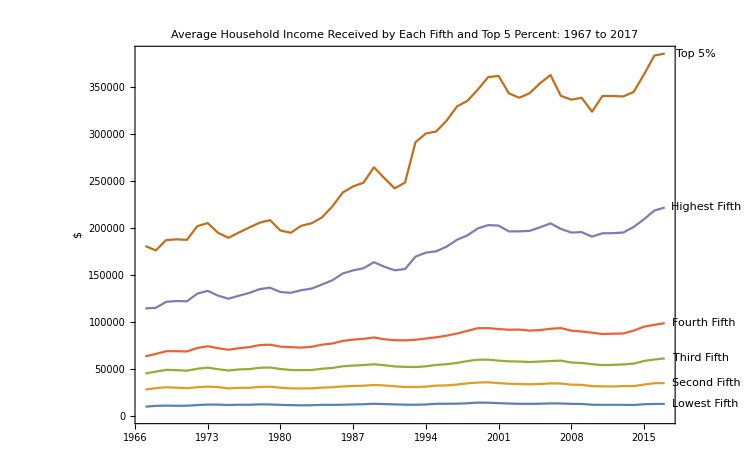

```mathematica
DateListPlot[cleanedData1,GridLines->Automatic,PlotLabel->Style[Framed["Average Household Income Received by Each Fifth and Top 5 Percent: 1967 to 2017"],15,White,Background->Blue], PlotTheme->"Detailed",FrameLabel->Automatic,ImageSize->750]
```

Graph with source information:

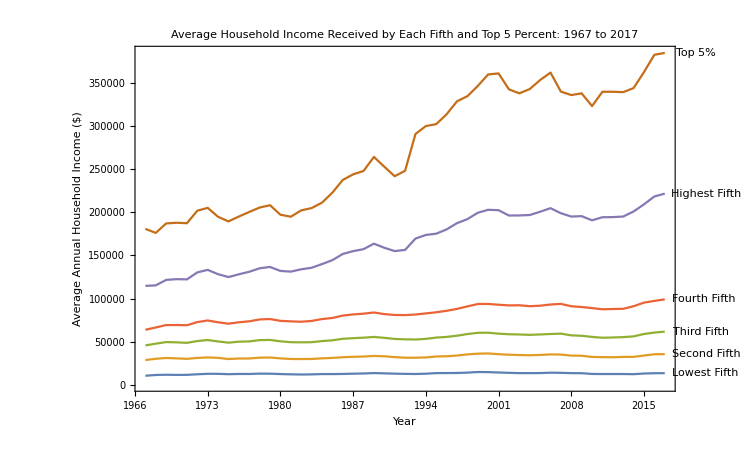
-Graphics-
[Source: U.S. Census Bureau. 2017. Historical Income Tables: Households, Table H-3.](https://www.census.gov/data/tables/time-series/demo/income-poverty/historical-income-households.html)

```mathematica
Column[{DateListPlot[cleanedData1,GridLines->Automatic,PlotLabel->Style[Framed["Average Household Income Received by Each Fifth and Top 5 Percent: 1967 to 2017"],15,White,Background->Blue],
PlotTheme->"Detailed",FrameLabel->{"Year","Average Annual Household Income ($)"},ImageSize->750],Hyperlink[Style["Source: U.S. Census Bureau. 2017. Historical Income Tables: Households, Table H-3.",FontFamily->"Helvetica",FontSize->10,FontColor->Gray,FontSlant->Italic],"https://www.census.gov/data/tables/time-series/demo/income-poverty/historical-income-households.html"]},Center]
```

```mathematica
Manipulate[BarChart[#[DateObject[{Year}]]&/@cleanedData,PlotRange->450000,ChartLabels->Keys[cleanedData],ChartStyle->"DarkRainbow",LabelingFunction->(Callout[#1,Automatic] &),PlotLabel->Style[Framed["Average Household Income Received by Each Fifth and Top 5 Percent (1967-2017)"],14,White,Background->Blue], PlotTheme->"Detailed",FrameLabel->Automatic,ImageSize->format],{{Year,2016},Sequence@@DateValue[MinMax[cleanedData[[1]]["DateList"][[1]]],"Year"],1},{{format,600,"Image Size"},300,900,25},SaveDefinitions->True]
```

Graph with source information:

```mathematica
Manipulate[Column[{BarChart[#[DateObject[{Year}]]&/@cleanedData,PlotRange->450000,ChartLabels->Keys[cleanedData],ChartStyle->"DarkRainbow",LabelingFunction->(Callout[#1,Automatic] &),PlotLabel->Style[Framed["Average Household Income Received by Each Fifth and Top 5 Percent (1967-2017)"],14,White,Background->Blue], PlotTheme->"Detailed",FrameLabel->{Automatic,"Average Annual Household Income ($)"},ImageSize->format],Hyperlink[Style["Source: U.S. Census Bureau. 2017. Historical Income Tables: Households, Table H-3.",FontFamily->"Helvetica",FontSize->10,FontColor->Gray,FontSlant->Italic],"https://www.census.gov/data/tables/time-series/demo/income-poverty/historical-income-households.html"]},Center],{{Year,2016},Sequence@@DateValue[MinMax[cleanedData[[1]]["DateList"][[1]]],"Year"],1},{{format,600,"Image Size"},300,900,25},SaveDefinitions->True]
```

Keys::invrl: The argument cleanedData is not a valid Association or a list of rules.

BarChart::ldata: cleanedData is not a valid dataset or list of datasets.

General::stop: Further output of BarChart::ldata will be suppressed during this calculation.

## 2. Unequal Income Growth

Below gives the accumulative growth in income

```mathematica
table//Length
```

```mathematica
100 (table[[1]]-table[[51]])/table[[51]];
```

```mathematica
100 (First[table[[]]]-Last[table[[]]])/Last[table[[]]];
```

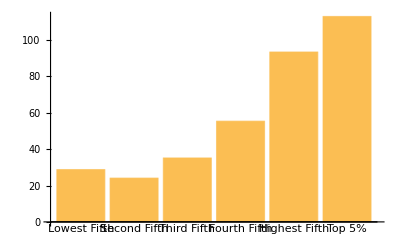

```mathematica
BarChart[100 (First[table[[]]]-Last[table[[]]])/Last[table[[]]],ChartLabels->Keys[cleanedData]]
```

```mathematica
HistoricalGrowthRates=Map[100 (table[[#]]-Last[table[[]]])/Last[table[[]]]&,Range[Length[table]-1]];
```

```mathematica
IncomeGrowthRate1=100*(#-#[DateObject[{1968}]])/#[DateObject[{1968}]]&/@cleanedData;
```

```mathematica
Manipulate[BarChart[#[DateObject[{Year}]]&/@IncomeGrowthRate1,PlotRange->{All,{-10,125}},AxesOrigin->{0,-8},ChartLabels->Keys[cleanedData],ChartStyle->"DarkRainbow",LabelingFunction->(Callout[#1,Above] &),PlotLabel->Style[Framed["Growth in Household Income Received by Each Fifth and Top 5 Percent (1968-2017)"],14,White,Background->Blue], PlotTheme->"Detailed",FrameLabel->{Automatic,"Real Income Growth 1968-2017 (Percent %)"},ImageSize->format],{{Year,2016},Sequence@@DateValue[MinMax[IncomeGrowthRate1[[1]]["DateList"][[1]]],"Year"],1},{{format,600,"Image Size"},300,700},SaveDefinitions->True]
```

Graph with source information:

```mathematica
Manipulate[Column[{BarChart[#[DateObject[{Year}]]&/@IncomeGrowthRate1,PlotRange->{All,{-10,125}},AxesOrigin->{0,-8},ChartLabels->Keys[cleanedData],ChartStyle->"DarkRainbow",LabelingFunction->(Callout[#1,Above] &),PlotLabel->Style[Framed["Growth in Household Income Received by Each Fifth and Top 5 Percent (1968-2017)"],14,White,Background->Blue], PlotTheme->"Detailed",FrameLabel->{Automatic,"Real Income Growth 1968-2017 (Percent %)"},ImageSize->format],Hyperlink[Style["Source: Author's calculations based on U.S. Census Bureau's Historical Income Tables (Table H-3). 
Note that 1968 is chosen as the base year because it is the year in which income inequality in the United States started to increase, as we will discuss in Chapter 10.",FontFamily->"Helvetica",FontSize->10,FontColor->Gray,FontSlant->Italic],"https://www.census.gov/data/tables/time-series/demo/income-poverty/historical-income-households.html"]},Center],{{Year,2016},Sequence@@DateValue[MinMax[IncomeGrowthRate1[[1]]["DateList"][[1]]],"Year"],1},{{format,600,"Image Size"},300,700},SaveDefinitions->True]
```

```mathematica
IncomeGrowthRate2=100*Differences[#]/TimeSeriesShift[#,Quantity[1, "Years"]]&/@cleanedData;
```

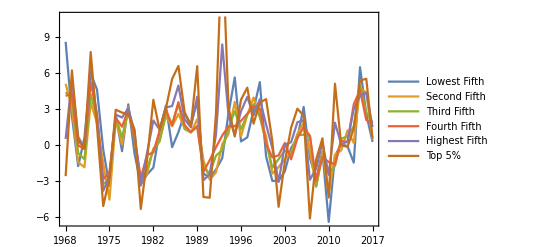

```mathematica
DateListPlot[IncomeGrowthRate2]
```

```mathematica
Manipulate[BarChart[#[DateObject[{Year}]]&/@IncomeGrowthRate2,PlotRange->{All,{Automatic,Automatic}},AxesOrigin->{Automatic,Automatic},ChartLabels->Keys[cleanedData],ChartStyle->"DarkRainbow",GridLines -> {None,{0}},LabelingFunction->(Callout[#1,Above] &),ImageSize->format],{{Year,2016},Sequence@@DateValue[MinMax[IncomeGrowthRate2[[1]]["DateList"][[1]]],"Year"],1},{{format,500,"Image Size"},300,700}]
```

Graph with source information:

```mathematica
Manipulate[Column[{BarChart[#[DateObject[{Year}]]&/@IncomeGrowthRate2,PlotRange->{All,{Automatic,Automatic}},AxesOrigin->{0,Automatic},ChartLabels->Keys[cleanedData],ChartStyle->"DarkRainbow",GridLines -> {None,Automatic},LabelingFunction->Top,PlotLabel->Style[Framed["Yearly Growth Rates in Household Income Received by Each Fifth and Top 5 Percent (1968-2017)"],14,White,Background->Blue], PlotTheme->"Detailed",FrameLabel->{Automatic,"Real Income Growth Rate (Percent %)"},ImageSize->format],Hyperlink[Style["Source: Author's calculations based on U.S. Census Bureau's Historical Income Tables (Table H-3).",FontFamily->"Helvetica",FontSize->10,FontColor->Gray,FontSlant->Italic],"https://www.census.gov/data/tables/time-series/demo/income-poverty/historical-income-households.html"]},Center],{{Year,2016},Sequence@@DateValue[MinMax[IncomeGrowthRate2[[1]]["DateList"][[1]]],"Year"],1},{{format,700,"Image Size"},500,800}]
```

## 3. Income Inequality – International Comparisons

```mathematica
giniIndices=EntityValue[EntityClass["Country","OrganizationForEconomicCooperationAndDevelopment"],Dated["GiniIndex",All],"EntityAssociation"];
windowedGiniIndices=DeleteCases[If[!Between[#["LastDate"],{DateObject[{2000}],DateObject[{2015}]}],Nothing,TimeSeriesWindow[#,{DateObject[{2000}],Now}]]&/@EntityValue[EntityClass["Country","OrganizationForEconomicCooperationAndDevelopment"],Dated["GiniIndex",All],"EntityAssociation"],Nothing];
```

```mathematica
#[DateObject[{2008}]]&/@windowedGiniIndices
```

```mathematica
If[Between[DateObject[{2008},"Instant"],{#["FirstDate"],#["LastDate"]}],#[DateObject[{2008}]],0]&/@windowedGiniIndices
```

```mathematica
Manipulate[BarChart[KeyValueMap[Labeled[#2,Style[#1,FontColor->Orange]]&,If[Between[DateObject[{year},"Instant"],{#["FirstDate"],#["LastDate"]}],#[DateObject[{year}]],0]&/@giniIndices],ChartStyle->"DarkRainbow",BarOrigin->Left,PlotLabel->Style[Framed["Gini Ratios in OECD Countries(1979-2017)"],14,White,Background->Gray], PlotTheme->"Detailed",FrameLabel->{Automatic,"Gini Coefficient"},ImageSize->format],{{year,2010,"Year"},1979,2017,1},{{format,600,"Image Size"},300,900,25}, SaveDefinitions->True]
```

## 4. Constrained Optimization and Utility Maximization

```mathematica
U1[x_,y_,α_]:=x^α y^(1-α);
Manipulate[
Show[
Plot3D[Labeled[U1[x,y,α],Style["Utility Hill",White],{5,5,10}],{x,0,10},{y,0,10},PlotTheme->"Web",AxesLabel->{"Orange", "Apple"},AxesStyle->White, Background->Black,Boxed->False,BoundaryStyle->Directive[White,Thick],ImageSize->format],
Graphics3D[{Blue,AbsolutePointSize[20],Point[{t,t,U1[t,t,α]}]}
]
],

{{α,.5,"Consumer's Preference (α)"},0,1},
{{format,500,"Image Size"},300,700},
{{t,5},0,10}, SaveDefinitions->True
]
```

## Budget Line and Maximizing Utility

```mathematica
Clear["Global`*"]
```

```mathematica
Manipulate[GraphicsGrid[{{Show[Plot3D[Labeled[U1[x,y,α],Style["Utility Hill",White],{5,5,10}],{x,0,10},{y,0,10},PlotTheme->"Web",AxesLabel->{"Apple", "Orange"},AxesStyle->White, Background->Black,Boxed->False,BoundaryStyle->Directive[White,Thick],PlotLabel->Style["Unconstrained Consumer Choices & 
Utility Hill", White, 14]],Graphics3D[{White,AbsolutePointSize[15],Tooltip[Point[{t,t,U1[t,t,α]}],"Robinson"]}
]],
Show[Plot[{Tooltip[(b/p2)-(p1/p2)*x, "Budget Line"], Tooltip[((b*(α^α)*((1-α)^(1-α))/((p1^α)*(p2^(1-α))))^(1/(1-α)))/(x^(α/(1-α))), "Indifference Curve"], Tooltip[(100/5)-(5/5)*x, "Budget Line"], Tooltip[((100*(0.5^0.5)*((1-0.5)^(1-0.5))/((5^0.5)*(5^(1-0.5))))^(1/(1-0.5)))/(x^(0.5/(1-0.5))), "Indifference Curve"], Tooltip[(1-α)*p1/(α*p2)*x, "Budget Expansion Path"], Tooltip[(1-0.5)*5/(0.5*5)*x, "Budget Expansion Path(MU_Apple/P_Apple=MU_Orange/P_Orange) "]},{x, 0, 40}, PlotStyle->{{White,Dashed}, {White,Dashed}, White, White, {White,Dashed}, {White,Dashed}}, PlotRange->{0, 45}, AxesLabel->{Style["Apple", 12], Style["Orange", 12]}, AxesStyle->White, Background->Black,PlotLabel->Style["Constrained Consumer Choices", White, 14],Filling->{1->Bottom}], 
ListPlot[{Tooltip[{{α*b/p1, (1-α)*b/p2}}, "New Utility-Maximizing Bundle"], Tooltip[{{0.5*100/5, (1-0.5)*100/5}}, "Initial Utility-Maximizing Bundle"]}, PlotStyle->{{Orange,PointSize[Large]},{White,PointSize[Large]}}]]}, {Show[Plot[{Tooltip[α*b/x, "Demand Curve for Apple"], Tooltip[0.5*100/x, "Demand Curve for Apple"]}, {x, 0, 40},PlotStyle->{{White,Dashed},White}, PlotRange->{{0, 42},{0,10}}, AxesLabel->{Style["Quantity", 12], Style["Price($)", 12]},AxesStyle->White, Background->Black, PlotLabel->Style["Demand for Apple",White, 14],
Epilog->{{White,{Dashed,Line[{{0.5*100/5,0},{0.5*100/5,5}}]},{Dashed,Line[{{0,5},{0.5*100/5,5}}]}},{{Orange,{Dashed,Line[{{α*b/p1,0},{α*b/p1,p1}}]},{Dashed,Line[{{0,p1},{α*b/p1,p1}}]}}}}
], 
ListPlot[{Tooltip[{{α*b/p1, p1}}, "Quantity Demanded; Price"], Tooltip[{{0.5*100/5, 5}}, "(Quantity Demanded; Price)"]}, PlotStyle->{{Orange,PointSize[Large]},{White,PointSize[Large]}}]], 
Show[Plot[{Tooltip[(1-α)*b/y, "Demand Curve for Orange"], Tooltip[(1-0.5)*100/y, "Demand Curve for Orange"]}, {y, 0, 40},PlotStyle->{{White,Dashed},White}, PlotRange->{{0, 42},{0,10}}, AxesLabel->{Style["Quantity", 12], Style["Price($)", 12]},AxesStyle->White, Background->Black, PlotLabel->Style["Demand for Orange",White, 14],
Epilog->{{White,{Dashed,Line[{{(1-0.5)*100/5,0},{(1-0.5)*100/5,5}}]},{Dashed,Line[{{0,5},{(1-0.5)*100/5,5}}]}},{{Orange,{Dashed,Line[{{(1-α)*b/p2,0},{(1-α)*b/p2,p2}}]},{Dashed,Line[{{0,p2},{(1-α)*b/p2,p2}}]}}}}
], 
ListPlot[{Tooltip[{{(1-α)*b/p2, p2}}, "Quantity Demanded; Price"], Tooltip[{{(1-0.5)*100/5, 5}}, "Quantity Demanded; Price"]}, PlotStyle->{{Orange,PointSize[Large]},{White,PointSize[Large]}}]]}}, 
Dividers->{False, All}, Frame->True, ImageSize->format], 
{{b, 150, "Budget"}, 0, 200,5,Appearance->"Labeled"}, 
{{p1, 5, "Price of Apple, P_a"}, 1, 10,Appearance->"Labeled"}, 
{{p2, 5, "Price of Orange, P_o"}, 1, 10,Appearance->"Labeled"}, 
Delimiter,
{{α, 0.5, "Robinson's Preferences"}, 0.1, .99,Appearance->"Labeled"},{{t,5, "The Motto of the Life on the Utility Hill: More is Better!"},0,10},{{format,700,"Image Size"},500,900},SaveDefinitions->True]
```

```mathematica
SetOptions[EvaluationNotebook[],WindowTitle-> "I.Aslantepe_Final_Project"]
```